### Query

Creates a layer between the solver and the game, which allows for flexibility.

```mathematica
QUEREVEALTILE=0;
QUETOGGLEFLAG=1;
QUETILETYPE=2;
QUEGETNEIGHBORS=3;
QUERYGRAPHICS=4;
QUERYCOMPLETE=5;
```

```mathematica
queryReveal[input_]:=revealTile[board,input⟦2⟧,input⟦3⟧,input⟦4⟧]
```

```mathematica
queryToggleFlag[input_]:=toggleFlag[board,input⟦2⟧,input⟦3⟧,input⟦4⟧]
```

```mathematica
queryTileType[input_]:=
Which[
board⟦input⟦2⟧,input⟦3⟧,input⟦4⟧,ISFLAGGEDI⟧==ISFLAGGED,{MINE,1},
board⟦input⟦2⟧,input⟦3⟧,input⟦4⟧,REVEALORNOT⟧==REVEALED,{NOTMINE,board⟦input⟦2⟧,input⟦3⟧,input⟦4⟧,NMINESI⟧},
True,-1
]
```

```mathematica
queryNeighbors[input_]:=board⟦input⟦2⟧,input⟦3⟧,input⟦4⟧,NEIGHBORDATAI⟧
```

```mathematica
queryGetDisplay[input_]:=displayBoard[board]
```

```mathematica
queryIsComplete[input_]:=isComplete[board]
```

```mathematica
(*Perform query on board. Can be updated as needed, but it must implement:
* revealTile[] - Needs an input of form {QUEREVEALTILE,sector, row, tile}. Return the output of revealTile[] and perform the operation on the given board
* toggleFlag[] - Needs an input of form {QUETOGGLEFLAG, sector, row, tile}. Turn on or off the flag and don't output anything
* getTile[] - Needs an input of form {QUETILETYPE, sector,row,tile}. Returns a number representing the tile, a -1 being unknown, 0 being revealed, and 1 being a flag.
*)
SetAttributes[queryBoard,HoldFirst]
queryBoard[input_]:=
Switch[input⟦1⟧,
QUEREVEALTILE,
Return[queryReveal[input]],
QUETOGGLEFLAG,
queryToggleFlag[input],
QUETILETYPE,
Return[queryTileType[input]],
QUEGETNEIGHBORS,
Return[queryNeighbors[input]],
QUERYGRAPHICS,
Return[queryGetDisplay[input]],
QUERYCOMPLETE,
Return[queryIsComplete[input]]
]
```

### Helper functions

#### Index conversions

```mathematica
flattenBoardIndex[index_,numRows_]:=
(*Add sector*)
(index⟦1⟧-1)numRows^2+
(*Add row*)
(index⟦2⟧-1)^2+
(*Add tile*)
index⟦3⟧
```

```mathematica
boardifyFlatIndex[RandomInteger[]]
```

```mathematica
RandomSample[{1,2,3},2]
```

{3,2}

```mathematica
indicesPlace=RandomSample[Table[If[i isn't off limits,i,Nothing],{i,Range[number of tiles]}],number of mines];
Do[
board[boardifyFlatIndex[index]]=mine
,{index,indicesPlace}
]
```

```mathematica
?RandomPermutation
```

```mathematica
boardifyFlatIndex[6,4]
```

{1,3,2}

```mathematica
boardifyFlatIndex[index_,numRows_]:=
Module[
{sector=Ceiling[index/numRows^2],
row=Ceiling[Sqrt[Mod[index-1,(numRows^2)]+1]]},
Return[{sector,row,index-(sector-1)numRows^2-(row-1)^2}]

]
```

```mathematica
flattenBoardIndex[{2,1,1},10]
```

101

```mathematica
Do[
If[flattenBoardIndex[boardifyFlatIndex[index,numRows]]≠index,Print[{index,numRows}]]
,{index,800}
,{numRows,10,50}
]
```

### Equation solvers

```mathematica
intersectionEqVec[eq1_,eq2_]:=Table[If[eq1⟦varPos⟧==eq2⟦varPos⟧&&eq1⟦varPos⟧==1,1,0],{varPos,Length@eq1-1}]
```

```mathematica
intersectionEqVec[{1,0,1,1,0,1,1,6},
{1,0,1,0,0,0,1,4}]
```

{1,0,1,0,0,0,1}

```mathematica
(*Solves a linear system of equations with binary variable values*)
cspSolve[binaryMat_]:=Module[
{binaryMatExtra=binaryMat,
newEqs={},
boolSols={},
varPosLst={},
curIndex=0,
changedSomething=True
},
While[changedSomething,
binaryMatExtra=DeleteDuplicates[binaryMatExtra];
changedSomething=False;
Do[
Do[
(*Bad cases*)
If[binaryMatExtra⟦eq1⟧==eq2||(!MemberQ[TakeDrop[binaryMatExtra⟦eq1⟧,Length@eq2-1]⟦1⟧,1]||!MemberQ[TakeDrop[eq2,Length@eq2-1]⟦1⟧,1]),Continue[]];
(*We can simplify*)
If[Append[intersectionEqVec[binaryMatExtra⟦eq1⟧,eq2],eq2⟦-1⟧]==eq2,
(*Subtract eq2 from eq1*)
binaryMatExtra⟦eq1⟧-=eq2;
changedSomething=True;
(*Get variable positions*)
varPosLst=Table[If[binaryMatExtra⟦eq1,i⟧==1,i,Nothing],{i,Length@binaryMatExtra⟦eq1⟧-1}];
(*All mines*)
If[Length[varPosLst]===binaryMatExtra⟦eq1,-1⟧,
Do[
AppendTo[newEqs,Table[0,{i,Length@eq2}]];
newEqs⟦-1,varPos⟧=1;
newEqs⟦-1,-1⟧=1;
changedSomething=True;
,{varPos,varPosLst}
]
];
(*All not mines*)
If[binaryMatExtra⟦eq1,-1⟧==0,
Do[
AppendTo[newEqs,Table[0,{i,Length@eq2}]];
newEqs⟦-1,varPos⟧=1;
newEqs⟦-1,-1⟧=0;
changedSomething=True;
,{varPos,varPosLst}
]
];
];
,{eq2,binaryMatExtra}
]
,{eq1,Length@binaryMatExtra}
];
(*Add in equations*)
Do[
AppendTo[binaryMatExtra,eq]
,{eq,newEqs}
];
];
binaryMatExtra=DeleteDuplicates[binaryMatExtra];
Return[binaryMatExtra]
]
```

```mathematica
pp={{{0,0},{0,2},{0,4},{5,3}},{{1,0},{1,2},{1,4},{1,3}},{{3,0},{3,2},{3,4},{3,3}},{{5,0},{5,2},{5,4},{5,3}}}
```

{{{0,0},{0,2},{0,4},{5,3}},{{1,0},{1,2},{1,4},{1,3}},{{3,0},{3,2},{3,4},{3,3}},{{5,0},{5,2},{5,4},{5,3}}}

```mathematica
pp[[-1]]
```

{{5,0},{5,2},{5,4},{5,3}}

```mathematica
Length@pp
```

4

```mathematica
Length@pp[[1]]
```

4

```mathematica
Length
```

```mathematica
(*Given a reduced linear system of equations in matrix form, returns a list of boolean values for each variable*)
findKnownSolutions[matReduceRes_]:=Module[
{valLst,varPosLst,lhs,rhs,definiteSols=Array[p,Length@matReduceRes⟦1⟧-1]},
Do[
lhs=TakeDrop[eq,Length@eq-1]⟦1⟧;
rhs=TakeDrop[eq,Length@eq-1]⟦2,1⟧;
Which[
(*Cannot glean information case*)
Length@Select[lhs,!(#==1||#==0)&]>0,
Continue[],
(*All mines case*)
Sum[lhs⟦i⟧,{i,Length@lhs}]==rhs,
Do[
If[lhs⟦i⟧==1,definiteSols⟦i⟧=1]
,{i,Length@lhs}
],
(*Revealed case*)
rhs==0,
Do[
If[lhs⟦i⟧==1,definiteSols⟦i⟧=0]
,{i,Length@lhs}
]

]
,{eq,matReduceRes}
];
Return[Table[If[solution===0||solution===1,solution,-1],{solution,definiteSols}]]
]
```

```mathematica
B=
{{1,1,0,0,2},
{0,0,1,1,1},
{1,1,0,1,2}};
A=
{2,
1,
2};
```

```mathematica
findKnownSolutions[cspSolve[B]]
```

{1,1,1,0}

### Solver interface

#### Main interface

```mathematica
(*
Returns a nested list in board form with each tile being of form {variableindex, knownvalue}.
knownvalue is -1 for unknown by default, but can be 0 or 1.
variableindex is an integer representing the position of this variable in the linear system matrix.
*)
initSolver[numRows_]:=
Module[
{indexMapping=1,
solverData,eqsPerTile,curTileType},
solverData=Table[
Table[
Table[{indexMapping++,Table[0,{i,8(numRows)^2+1}],Table[0,{i,8(numRows)^2+1}]},{tile,2row-1}
],{row,numRows}],{sector,8}
];
Do[
curTileType=queryBoard[{QUETILETYPE,sectorI,rowI,tileI}];
If[curTileType==-1,Continue[]];
createTileEq[solverData,sectorI,rowI,tileI];

,{sectorI,8}
,{rowI,numRows}
,{tileI,2rowI-1}
];
Return[solverData]
]
```

```mathematica
SetAttributes[createTileEq,HoldFirst];
createTileEq[solverData_,sector_,row_,tile_]:=
Module[
{newEq1=Table[0,{i,8(Length@solverData⟦1⟧)^2+1}],
qTileData=queryBoard[{QUETILETYPE,sector,row,tile}],
newEq2=Table[0,{i,8(Length@solverData⟦1⟧)^2+1}]},
If[qTileData==-1,Return[]];
If[
qTileData⟦1⟧==MINE,
(*MINE CASE*)
newEq1⟦flattenBoardIndex[{sector,row,tile},Length@solverData⟦1⟧]⟧=1;
newEq1⟦Length@newEq1⟧=1;
];
If[
qTileData⟦1⟧==NOTMINE,
(*REVEALED CASE*)
newEq1⟦flattenBoardIndex[{sector,row,tile},Length@solverData⟦1⟧]⟧=1;
newEq1⟦Length@newEq1⟧=0;
Do[
newEq2⟦flattenBoardIndex[neighbor,Length@solverData⟦1⟧]⟧=1
,{neighbor,queryBoard[{QUEGETNEIGHBORS,sector,row,tile}]}
];
newEq2⟦Length@newEq2⟧=qTileData⟦2⟧
];
solverData⟦sector,row,tile,2⟧=newEq1;
solverData⟦sector,row,tile,3⟧=newEq2
]
```

```mathematica
(*Analyze tiles in batches rather than as a lump solve*)
analyzeEqsBatches[solverData_,corrPosBatches_]:=
Module[
{batchSols=Table[analyzeEqs[solverData,batch],{batch,corrPosBatches}],
knowns=Table[-1,{i,8(Length@solverData⟦1⟧)^2}]},
(* Compile known values *)
Do[
knowns⟦tile⟧=Max[knowns⟦tile⟧,batchSol⟦tile⟧]
,{tile,Length@knowns}
,{batchSol,batchSols}
];
Return[knowns]
]
```

```mathematica
(*Analyze the given positions by creating equations representing them and solving*)
analyzeEqs[solverData_,corrPos_]:=
Module[
{sysEqs=DeleteCases[DeleteDuplicates[chooseTiles[solverData,corrPos]],Table[0,{i,8(Length@solverData⟦1⟧)^2}]],
reducedSols,eqLHS,eqRHS,lhs1s,curEq=1,neighborType},
If[Length@sysEqs==0,Return[]];
reducedSols=cspSolve[sysEqs];
Return[findKnownSolutions[reducedSols]]
]
```

```mathematica
chooseTiles[solverInterface_,chosenTiles_]:=
Join[
Table[solverInterface⟦tile⟦1⟧,tile⟦2⟧,tile⟦3⟧,2⟧,{tile,chosenTiles}],
Table[solverInterface⟦tile⟦1⟧,tile⟦2⟧,tile⟦3⟧,3⟧,{tile,chosenTiles}],
Join@@Table[If[queryBoard[Prepend[neighbor,QUETILETYPE]]=!=-1,solverInterface⟦neighbor⟦1⟧,neighbor⟦2⟧,neighbor⟦3⟧,2⟧,Nothing],{tile,chosenTiles},{neighbor,queryBoard[{QUEGETNEIGHBORS,tile⟦1⟧,tile⟦2⟧,tile⟦3⟧}]}]
]
```

```mathematica
(*Perform clicks based on the result of analyzeEqs*)
makeClicks[analResult_]:=
Do[
(*Case no changes to make*)
If[analResult⟦index⟧===-1||queryBoard[Prepend[boardifyFlatIndex[index,Sqrt[Length@analResult/8]],QUETILETYPE]]=!=-1,Continue[]] ;
If[analResult⟦index⟧==1,
queryBoard[Prepend[boardifyFlatIndex[index,Sqrt[Length@analResult/8]],QUETOGGLEFLAG]],
If[queryBoard[Prepend[boardifyFlatIndex[index,Sqrt[Length@analResult/8]],QUEREVEALTILE]]==False,Print["You dumb bro"]
]
]
,{index,Length@analResult}
]
```

```mathematica
SetAttributes[interfaceNext,HoldFirst]
interfaceNext[solverInterface_,heuristicFunc_,modBoard_]:=Module[
{(*Call the heuristic function*)
chosenTiles=heuristicFunc[solverInterface],analResult,clickedTiles},
analResult=analyzeEqs[solverInterface,chosenTiles];
If[modBoard,
makeClicks[analResult];
];
solverInterface=initSolver[Length@solverInterface⟦1⟧];
Return[analResult]
]
```

```mathematica
SetAttributes[autoSolve,HoldFirst]
autoSolve[solverInterface_,heuristicFunc_]:=
Module[
{lastAnal=googoo,
newAnal=interfaceNext[solverInterface,heuristicFunc,True],
steps={},
stepNumber=1},
While[lastAnal=!=newAnal,
Print["Step "<>ToString[stepNumber++]];
lastAnal=newAnal;
AppendTo[steps,queryBoard[{QUERYGRAPHICS}]];
newAnal=interfaceNext[solverInterface,heuristicFunc,True]
];
Return[steps]
]
```

```mathematica
(*With guessing*)
autoSolve[solverInterface_,heuristicFunc_,guessHeurFunc_]:=Module[
{lastAnal=googoo,
newAnal=interfaceNext[solverInterface,heuristicFunc,True],
steps={},
stepNumber=1},
While[!queryBoard[{QUERYCOMPLETE}],
Print["Step "<>ToString[stepNumber++]];
lastAnal=newAnal;
AppendTo[steps,queryBoard[{QUERYGRAPHICS}]];
newAnal=interfaceNext[solverInterface,heuristicFunc,True];
If[newAnal==lastAnal,
makeClicks[guessHeurFunc[solverInterface]]
]
];
Return[steps]
]
```

#### Heuristic functions

```mathematica
unknownAround[tile_]:=
Module[{hasUnknown=False},
Do[
If[queryBoard[Prepend[neighbor,QUETILETYPE]]==-1,hasUnknown=True]
,{neighbor,queryBoard[{QUEGETNEIGHBORS,tile⟦1⟧,tile⟦2⟧,tile⟦3⟧}]}
];
Return[hasUnknown]
]
```

```mathematica
testHeur[solverInterface_]:=
Module[
{numRows=Length@solverInterface⟦1⟧},
Table[If[
(*It is revealed and there are unknowns around*)unknownAround[boardifyFlatIndex[index,numRows]]&&
(queryBoard[Prepend[boardifyFlatIndex[index,numRows],QUETILETYPE]]=!=-1&&queryBoard[Prepend[boardifyFlatIndex[index,numRows],QUETILETYPE]]⟦1⟧==NOTMINE),boardifyFlatIndex[index,numRows],Nothing],{index,8(numRows)^2}]
]
```

```mathematica
moreEfficientHeur[solverInterface_,tilesToUse_]:=
Module[
{tilesLeftUse=tilesToUse,beginTile=boardifyFlatIndex[RandomInteger[1,8(Length@solverInterface⟦1⟧)^2]],numRows=Length@solverInterface⟦1⟧},
AppendTo[beginTile,RandomInteger[1,2beginTile⟦2⟧-1]];
While[!(unknownAround[beginTile]&&
(queryBoard[Prepend[beginTile,QUETILETYPE]]=!=-1&&queryBoard[Prepend[beginTile,QUETILETYPE]]⟦1⟧==NOTMINE)),
beginTile=boardifyFlatIndex[RandomInteger[1,8(Length@solverInterface⟦1⟧)^2]];
]
]
```

```mathematica
testGuessHeur[solverInterface_]:=boardifyFlatIndex[RandomInteger[{1,8(Length@solverInterface⟦1⟧)^2}]]
```

#### Examples

```mathematica
solverInterface=initSolver[6];
```

```mathematica
interfaceNext[solverInterface,testHeur,True];
```

```mathematica
Graphics[displayBoard[board]]
```

```mathematica
Sum[Table[]]
```

```mathematica
board⟦2,3,1,MINETYPEI⟧
```

0

```mathematica
Manipulate[
Graphics[stepsSolve⟦i⟧]
,{i,1,Length@stepsSolve,1}
]
```

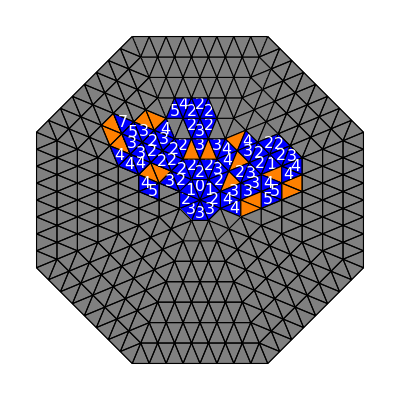

```mathematica
Graphics[displayBoard[board]]
```

```mathematica
solverInterface=initSolver[6]
```

{{1},{{1},4,{1}},4,{1},{{1},{{1},1,1},{{1},3,1},{{1},5,1},{{1},7,1},{1}}}
 |  |  |  |

```mathematica
interfaceNext[solverInterface,testHeur,True]
```

{0,0,0,0,1,0,0,0,1,0,0,0,0,1,1,-1,-1,0,0,0,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,0,0,0,0,0,0,0,0,1,-1,-1,-1,0,1,1,-1,-1,-1,-1,0,0,0,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,0,0,0,0,0,0,0,0,0,-1,0,1,0,0,0,0,-1,-1,-1,0,0,0,0,0,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,0,0,0,0,1,0,0,0,0,0,0,0,0,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,0,0,1,0,0,1,0,0,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,0,0,0,1,-1,1,0,0,0,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,0,0,0,0,0,0,0,0,1,-1,0,0,0,0,0,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,0,0,0,0,1,1,0,1,1,-1,-1,-1,-1,-1,0,0,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1}

```mathematica
interfaceNext[solverInterface,testHeur,True]
```

$Aborted